## 1

```mathematica
Clear["Global`*"];
dim=5/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
Hmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_]:=({{0, (√5)/2 ⅇ^(-ⅈ ϕ1), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ1), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}});
Iplus5half2=Ix3half2+I*Iy3half2;
Iminus5half2=Ix3half2-I*Iy3half2;
UHmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_]:=N[MatrixExp[-I*Hmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5]*t] ]
IniPhi={{1},{0},{0},{0},{0},{0}};

(*StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi*)

StateθϕInitial[θ_,ϕ_]:={{Cos[θ/2]^5},{√5 ⅇ^(ⅈ ϕ) Cos[θ/2]^4 Sin[θ/2]},{1/4 √(5/2) ⅇ^(2 ⅈ ϕ) Csc[θ/2] Sin[θ]^3},{1/2 √(5/2) ⅇ^(3 ⅈ ϕ) Sin[θ/2] Sin[θ]^2},{1/2 √5 ⅇ^(4 ⅈ ϕ) Sin[θ/2]^3 Sin[θ]},{ⅇ^(5 ⅈ ϕ) Sin[θ/2]^5}}

StateEvo[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_,θ_,ϕ_]:=N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,t].StateθϕInitial[θ,ϕ]]
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
Chop[N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]]
]
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
If[Chop[N[First[Flatten[yVal]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],Chop[N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]]
]

In1[state_]:=Chop[N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]]
In2[state_]:=Chop[N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]]
In1n2plusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]]
In1n2minusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]]
In1n2n2n1[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]]
ξSqure[state_]:=Chop[N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]],10^-8]
```

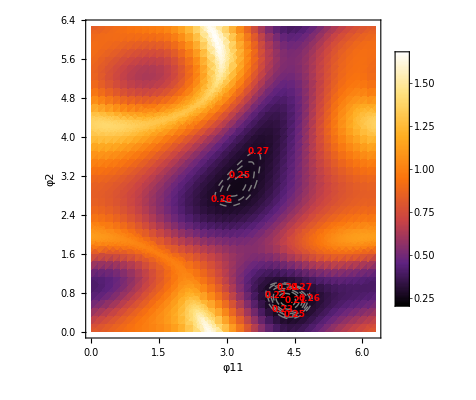

```mathematica
AA1=Show[(*主密度图-保持完整显示*)DensityPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,Pi/2,Pi-φ2,Pi-φ11,0.408,Pi/2,Pi/2]]]]/(5/2),{φ11,0,2Pi},{φ2,0,2Pi},PlotLegends->Automatic,ColorFunction->"SunsetColors",PlotPoints->40,FrameLabel->{"φ11","φ2"},LabelStyle->{Bold,12}],(*青色区域:仅填充<0.25 区域，不遮挡其他部分*)ContourPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,Pi/2,Pi-φ2,Pi-φ11,0.408,Pi/2,Pi/2]]]]/(5/2),{φ11,0,2Pi},{φ2,0,2Pi},Contours->Range[0.15,0.27,0.01],(*仅<0.5 的等高线值*)ContourLabels->(Text[Style[#3,9,Bold,Red],{#1,#2}]&),(*红色标签*)ContourStyle->Directive[Gray,Thick,Dashed],(*黑色虚线*)PlotPoints->40,ContourShading->None  (*🔥 关键修复:禁用背景填充!*)]]
```

```mathematica
(*假设 ξSquare 是您自定义的平方函数，例如：ξSquare[x_]:=Abs[x]^2*)(*请确保 StateEvo 已正确定义*)Show[(*主密度图*)DensityPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,Pi/2,Pi-φ2,Pi-φ11,0.408,Pi/2,Pi/2]]]]/(5/2),{φ11,-Pi,Pi},{φ2,-Pi,Pi},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotPoints->50,FrameLabel->{"φ11","φ2"},LabelStyle->{Bold,12}],(*叠加红色区域:值<0.25 的区域*)ContourPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,Pi/2,Pi-φ2,Pi-φ11,0.408,Pi/2,Pi/2]]]]/(5/2),{φ11,-Pi,Pi},{φ2,-Pi,Pi},Contours->{0.3},ContourShading->{Red,None},(*小于 0.25 的区域填充红色*)ContourStyle->Directive[Black,Dashed],(*等高线样式*)PlotPoints->50],(*添加等高线标注*)ContourPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,Pi/2,Pi-φ2,Pi-φ11,0.408,Pi/2,Pi/2]]]]/(5/2),{φ11,-Pi,Pi},{φ2,-Pi,Pi},Contours->10,(*10 条等高线*)ContourLabels->All,ContourStyle->Black,PlotPoints->50]]
```

-Graphics-